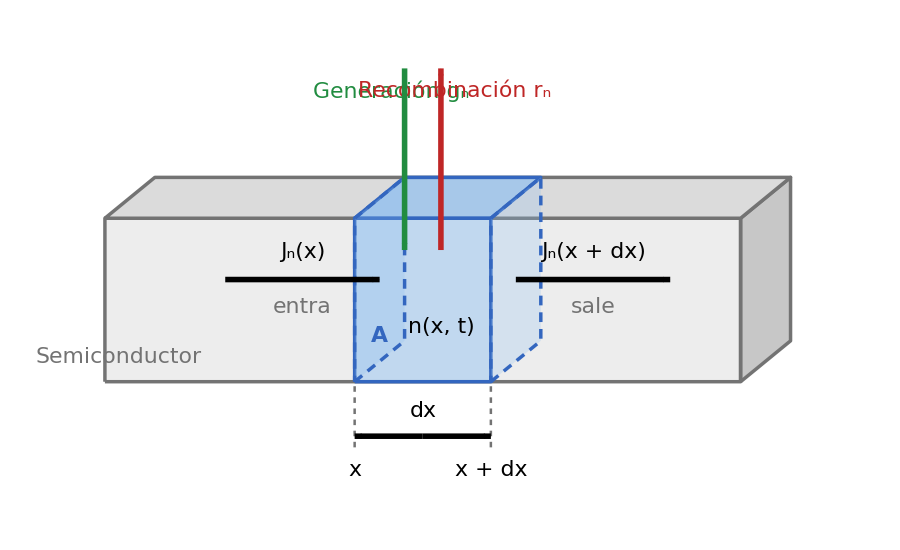

```mathematica
diagramaContinuidad = Module[
  {fs, cAzul, cAzulB, cVerde, cRojo, cGris, hh, px, py, xb0, xb1, xs0, xs1,
   xm, yc, ins, tx, flecha, cara, caraF, caraT, caraS},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;   (* tamaño de fuente único para todo el gráfico *)
  cAzul  = RGBColor[0.55, 0.75, 0.95];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cVerde = RGBColor[0.13, 0.55, 0.25];  cRojo  = RGBColor[0.75, 0.15, 0.15];
  cGris  = GrayLevel[0.45];

  (* ---------- Geometría (proyección oblicua) ---------- *)
  hh = 3.6;                    (* altura de la barra *)
  {px, py} = {1.1, 0.9};       (* desplazamiento por profundidad *)
  {xb0, xb1} = {1.5, 15.5};    (* extremos de la barra *)
  {xs0, xs1} = {7.0, 10.0};    (* elemento diferencial: de x a x + dx *)
  xm = (xs0 + xs1)/2;          (* centro del elemento *)
  yc = hh/2 + py/2;            (* altura del centro de las secciones A *)

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  tx[expr_, pos_, al_, col_: Black] := Text[Style[expr, fs, col], pos, al];
  flecha[p1_, p2_, col_, s_: 0.028] :=
    {col, AbsoluteThickness[4], Arrowheads[s], Arrow[{p1, p2}]};

  caraF[x0_, x1_] := {{x0, 0}, {x1, 0}, {x1, hh}, {x0, hh}};
  caraT[x0_, x1_] := {{x0, hh}, {x1, hh}, {x1 + px, hh + py}, {x0 + px, hh + py}};
  caraS[x_] := {{x, 0}, {x + px, py}, {x + px, hh + py}, {x, hh}};
  cara[pts_, relleno_, op_, borde_] :=
    {{Opacity[op, relleno], EdgeForm[None], Polygon[pts]},
     {borde, AbsoluteThickness[2.5], Line[Append[pts, First[pts]]]}};

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* barra de semiconductor *)
    cara[caraS[xb1], GrayLevel[0.78], 1, cGris],
    cara[caraT[xb0, xb1], GrayLevel[0.86], 1, cGris],
    cara[caraF[xb0, xb1], GrayLevel[0.93], 1, cGris],
    tx["Semiconductor", {xb0 + 0.3, 0.55}, {-1, 0}, cGris],

    (* elemento diferencial: caras visibles y secciones A (ocultas, discontinuas) *)
    cara[caraT[xs0, xs1], cAzul, 0.65, cAzulB],
    cara[caraF[xs0, xs1], cAzul, 0.45, cAzulB],
    Table[
     {{Opacity[0.25, cAzul], EdgeForm[None], Polygon[caraS[xx]]},
      {cAzulB, AbsoluteThickness[2.5], AbsoluteDashing[{7, 5}],
       Line[Append[caraS[xx], First[caraS[xx]]]]}},
     {xx, {xs0, xs1}}],
    ins[Style["A", Bold], {xs0 + px/2, 1.0}, cAzulB],
    ins["n(x, t)", {xm + 0.4, 1.2}],

    (* corrientes: entra por x, sale por x + dx *)
    flecha[{xs0 + px/2 - 3.4, yc}, {xs0 + px/2, yc}, Black],
    flecha[{xs1 + px/2, yc}, {xs1 + px/2 + 3.4, yc}, Black],
    ins[Row[{Subscript["J", "n"], "(x)"}], {xs0 + px/2 - 1.7, yc + 0.6}],
    ins[Row[{Subscript["J", "n"], "(x + dx)"}], {xs1 + px/2 + 1.7, yc + 0.6}],
    tx["entra", {xs0 + px/2 - 1.7, yc - 0.6}, {0, 0}, cGris],
    tx["sale", {xs1 + px/2 + 1.7, yc - 0.6}, {0, 0}, cGris],

    (* generación (entra) y recombinación (sale) *)
    flecha[{xm - 0.4, 6.9}, {xm - 0.4, 2.9}, cVerde],
    flecha[{xm + 0.4, 2.9}, {xm + 0.4, 6.9}, cRojo],
    tx[Row[{"Generación ", Subscript["g", "n"]}], {xm - 0.7, 6.4}, {1, 0}, cVerde],
    tx[Row[{"Recombinación ", Subscript["r", "n"]}], {xm + 0.7, 6.4}, {-1, 0}, cRojo],

    (* cota del espesor dx *)
    {cGris, AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
     Line[{{xs0, -0.1}, {xs0, -1.55}}], Line[{{xs1, -0.1}, {xs1, -1.55}}]},
    flecha[{xm, -1.2}, {xs0, -1.2}, Black, 0.02],
    flecha[{xm, -1.2}, {xs1, -1.2}, Black, 0.02],
    ins["dx", {xm, -0.65}],
    ins["x", {xs0, -1.95}],
    ins["x + dx", {xs1, -1.95}]
   },
   ImageSize -> 900,
   PlotRange -> {{1.0, 17.2}, {-2.6, 7.3}},
   PlotRangePadding -> None,
   AspectRatio -> Automatic,
   Background -> White]
];
diagramaContinuidad
```